Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 4. Julia e Mandelbrot sets, paesaggi frattali

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 4.2 (Insieme di Mandelbrot e dinamica della mappa quadratica).

### Testo dell’esercizio

Investigare la relazione tra la struttura dell’insieme di Mandelbrot e le orbite periodiche attrattive del sistema dinamico discreto dato dalle iterazioni del polinomio P_c(z)=z^2+c. Si può fare una e/o l’altra delle cose seguenti.

Produrre per qualche n=1,2,3,… (arrivare a quel che si desidera o si riesce) un’immagine o un’animazione che, per un opportuno valore di c, dipendente da n, evidenzi l’esistenza di un’orbita periodica attrattiva di P_c di periodo n all’interno di K_c. Evidenziare nel Mandelbrot i valori usati di c.

Posizionare un locator nel Mandelbrot che legga c e produca a fianco un disegno di K_c con l’orbita periodica attrattiva al suo interno.

### Svolgimento

Visualizziamo il rapporto tra l’appartenenza di un punto a un certo lobo dell’insieme di Mandelbrot e il corrispondente insieme di Julia. Rispetto alla notazione dei parametri usata a lezione è stato aggiunto jprec, che indica il numero di applicazioni effettuate delle due inverse di P_c: per jprec ≥ 18 abbiamo incontrato problemi di lag; per jprec < 10 i punti si rarefanno oltremodo in alcune conformazioni. Questa implementazione non può individuare esplicitamente orbite con più di 10 punti attrattori e può generare errori di overflow se si pone il locator al di fuori del Mandelbrot. Sempre per ragioni di lag, risulta comodo cancellare l’output nel caso si voglia usare un’altra implementazione.

```mathematica
confrontoLinea[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_,jprec_]:=DynamicModule[
{
c0={-1.,0.},
j=Compile[
{{z,_Complex},{n,_Integer},{c,_Complex}},
Module[{k=0,w=z,r=.5+Sqrt[.25+Abs[c]]},While[Abs[w]<r&&k<nit,w=w^2+c;k++];0.7 (k+1)/(1+n)]
],
mgrid,mset,lst
},
mgrid[{xmin2_,xmax2_,ymin2_,ymax2_},ndiv2_,nit2_]:=ParallelTable[j[0,nit2,cx+I cy],{cy,ymin2,ymax2,(ymax2-ymin2)/ndiv2},{cx,xmin2,xmax2,(xmax2-xmin2)/ndiv2}];
mset[{xmin2_,xmax2_,ymin2_,ymax2_},ndiv2_,nit2_]:=Graphics@Raster[mgrid[{xmin2,xmax2,ymin2,ymax2},ndiv2,nit2],{{xmin2,ymin2},{xmax2,ymax2}},ColorFunction->Function[a,If[a==0.7,Black,ColorData[{"SunsetColors","Reverse"}][a]]]];
GraphicsRow[
{
Show[
mset[N@{xmin,xmax,ymin,ymax},ndiv,nit],
Graphics[Locator[Dynamic@c0,Graphics[{Red,Point[{0,0}],Circle[]},ImageSize->12]]],
Frame->True,ImageSize->Scaled[0.4],PlotLabel->Dynamic@TraditionalForm[Chop[Complex@@c0]]
],
Dynamic@Show[ListPlot[{Re[#],Im[#]}&/@Function[{c},Nest[Function[{l},Flatten[Function[{z},{-√(z-c),√(z-c)}]/@l]],{-0.1},jprec]][Complex@@c0],ImageSize->Scaled[0.5],Axes->False,Frame->True,PlotRange->{{-1.8,1.8},{-1.3,1.3}},AspectRatio->Automatic,PlotStyle->Black],ListPlot[{Re[#],Im[#]}&/@Take[NestList[Complex@@c0+#^2&,0,75],-10],PlotStyle->Red]]
},
ImageSize->Full
]
]
```

```mathematica
confrontoLinea[{-2.,1.5,-1.5,1.5},1000,50,12]
```

Come visto anche a lezione, scegliere c nel cardioide centrale fa sì che l’orbita attrattiva abbia un solo attrattore, mentre scegliere c nel lobo cui appartiene -1 corrisponde ad orbite con due attrattori; per ottenere orbite con tre attrattori, si può scegliere c nei lobi cui appartengono -1/10-3/4 ⅈ e -1/10+3/4 ⅈ.
Ragionando in modo analogo ed avvalendosi del costrutto interattivo, si trova che per individuare insiemi di Julia con orbite attrattive con quattro attrattori occorre scegliere c nel lobi di -13/10, 3/10-ⅈ/2 e 3/10+ⅈ/2.

#### Altre implementazioni

La seguente implementazione prende le funzioni sviluppate a lezione e le usa per fare un confronto tra il Mandelbrot e l’insieme di Julia munito di colori. Essa, però, è altamente inefficiente, perché dà risposte in tempi ragionevoli solo per ndiv ≤ 150 e per nit ≤ 15.

confrontoColore[{xmin_,xmax_,ymin_,ymax_},ndiv_,nit_]:=DynamicModule[
{
z0={-1.,0.},
j=Compile[
{{z,_Complex},{n,_Integer},{c,_Complex}},
Module[{k=0,w=z,r=.5+Sqrt[.25+Abs[c]]},While[Abs[w]<r&&k<nit,w=w^2+c;k++];0.7 (k+1)/(1+n)]
],
jgrid,jset,mgrid,mset
},
jgrid[{xmin2_,xmax2_,ymin2_,ymax2_},ndiv2_,nit2_,c_]:=ParallelTable[
j[x+I y,nit2,c],{y,ymin2,ymax2,(ymax2-ymin2)/ndiv2},{x,xmin2,xmax2,(xmax2-xmin2)/ndiv2}
];
jset[{xmin2_,xmax2_,ymin2_,ymax2_},ndiv2_,numit_,c_]:=Graphics@Raster[
jgrid[{xmin2,xmax2,ymin2,ymax2},ndiv2,numit,c],
{{xmin2,ymin2},{xmax2,ymax2}},
ColorFunction→Function[a,If[a==0.7,Black,ColorData[{"SunsetColors","Reverse"}][a]]]
];
mgrid[{xmin2_,xmax2_,ymin2_,ymax2_},ndiv2_,nit2_]:=ParallelTable[j[0,nit2,cx+I cy],{cy,ymin2,ymax2,(ymax2-ymin2)/ndiv2},{cx,xmin2,xmax2,(xmax2-xmin2)/ndiv2}];
mset[{xmin2_,xmax2_,ymin2_,ymax2_},ndiv2_,nit2_]:=Graphics@Raster[mgrid[{xmin2,xmax2,ymin2,ymax2},ndiv2,nit2],{{xmin2,ymin2},{xmax2,ymax2}},ColorFunction→Function[a,If[a==0.7,Black,ColorData[{"SunsetColors","Reverse"}][a]]]];
GraphicsRow[
{
Show[
mset[N@{xmin,xmax,ymin,ymax},ndiv,nit],
Graphics[Locator[Dynamic@z0,Graphics[{Red,Point[{0,0}],Circle[]},ImageSize→12]]],
Frame→True,ImageSize→Scaled[0.4],PlotLabel→Dynamic@TraditionalForm[Chop[Complex@@z0]]
],
Dynamic@Show[
jset[{xmin,xmax,ymin,ymax},ndiv,nit,Complex@@z0],
ListPlot[{Re[#],Im[#]}&/@Take[NestList[Complex@@z0+#^2&,0,50],-10],PlotRange→{{xmin,xmax},{ymin,ymax}},PlotStyle→Red],
Frame→True,ImageSize→Scaled[0.4]
]
},
ImageSize→Full
]
]

Il problema scompare del tutto se alle funzioni sviluppate a lezione si sostituiscono le funzioni built-in del Wolfram Language.

```mathematica
confrontoBuiltin[{xmin_,xmax_,ymin_,ymax_}]:=DynamicModule[
{
z0={-1.,0.}
},
GraphicsRow[
{
Show[
MandelbrotSetPlot[{xmin+I ymin,xmax+I ymax},ImageResolution->1000],
Graphics[Locator[Dynamic@z0,Graphics[{Red,Point[{0,0}],Circle[]},ImageSize->12]]],
Frame->True,ImageSize->Scaled[0.4],PlotLabel->Dynamic@TraditionalForm[Chop[Complex@@z0]]
],
Dynamic@Show[
JuliaSetPlot[Complex@@z0,ImageResolution->1000],
ListPlot[{Re[#],Im[#]}&/@Take[NestList[Complex@@z0+#^2&,-0.1,75],-10],PlotRange->{{xmin,xmax},{ymin,ymax}},PlotStyle->Red],
Frame->True,ImageSize->Scaled[0.5]
]
},
ImageSize->Full
]
]
```

```mathematica
confrontoBuiltin[{-2.,1.5,-1.5,1.5}]
```

## Esercizio 4.3 (Paesaggi frattali e dimensione box-counting).

### Testo dell’esercizio

Costruire un (bel) paesaggio frattale.

Determinare la dimensione del box-counting di qualche paesaggio costruito con diversi valori dell’esponente α del fattore di riscalamento k=2^α della variazione casuale delle altezze.

Si riesce a formulare un’ipotesi sulla dipendenza della dimensione box-counting dall’esponente α?

### Svolgimento

```mathematica
pmedio[lst_,r_,α_,n_]:={lst⟦1⟧,(lst⟦1⟧+lst⟦2⟧)/2+RandomReal[{-1/2,1/2}]r 2^(-α n)}
riga[lst_,r_,α_,n_]:=Append[pmedio[#,r,α,n]&/@Partition[lst,2,1]//Flatten,Last[lst]]
f[matr_,r_,α_,n_]:=(riga[#,r,α,n]&/@Transpose[riga[#,r,α,n]&/@matr])ᵀ
f2[matr_,r_,α_,n_]:=Fold[f[#1,r,α,#2]&,matr,Range[n]]
f3[matr_,r_,α_,liv_,nit_]:=Map[Max[#,liv]&,f2[matr,r,α,nit],{2}]
fig[matr_,r_,α_,liv_,nit_]:=ListPlot3D[f3[matr,r,α,liv,nit],Mesh->None,Boxed->False,Axes->False,PlotRange->All,ColorFunction->Function[{x,y,z},If[z==0,ColorData["AlpineColors"][z],ColorData["AlpineColors"][z+0.2]]],Lighting->{{"Point",White,{Length@matr,Length[matr//First],2Max[matr]}}}]
```

```mathematica
fig[RandomInteger[128,{5,5}],8.,.6,64,6]
```

-Graphics3D-

```mathematica
triple[matr_]:=Flatten[Table[{m,n,matr[[m,n]]},{m,1,Length@matr},{n,1,Length[matr//First]}],1]
```

```mathematica
scatole[data_,div_,limiti_]:=Length[Union[Floor[((div-1)(#-limiti⟦1⟧))/(limiti⟦2⟧-limiti⟦1⟧)&/@triple[data]]]]
```

```mathematica
scatole[({{1, 0, 5}, {65, 2, 6}, {4, 5, 6}}),1,{{1,1,1},{3,3,70}}]
```

1

```mathematica
contaScatole[data_,{nmin_,nmax_}]:=scatole[data,#,{{1,1,Min[data]},{Length[data],Length[data//First],Max[data]}}]&/@Table[2^n,{n,nmin,nmax}]
```

```mathematica
coeff[data_,{nmin_,nmax_}]:=Fit[{Range[nmin,nmax],Log2@contaScatole[data,{nmin,nmax}]}ᵀ,{1,x},x]
```

```mathematica
m=f3[RandomInteger[128,{5,5}],12.,.6,64,6];
```

```mathematica
coeff[m,{1,6}]
```

0.472814+2.23984 x

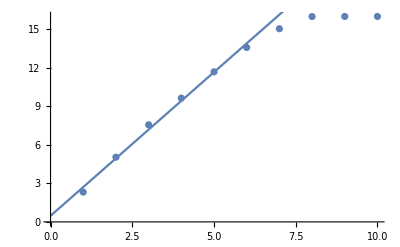

```mathematica
Show[ListPlot[Log2@contaScatole[m,{1,10}]],Plot[coeff[m,{1,6}]//Evaluate,{x,0,10}]]
```

```mathematica
min={{0.,0.6},{0.2,-0.1}};
data=f3[min,1.,0.5,0,9];
coeff[data,{1,7}]
```

0.136158+2.4395 x

```mathematica
bCDim[count_,{nmin_,nmax_}]:=D[Fit[Take[Log2@count,{nmin,nmax}],{1,x},x],x]
```

```mathematica
min={{0.,0.6,0.4},{0.2,0,-0.1},{0.1,0.2,0.4}};
prove=Table[Table[f3[min,1.,α,0.,5],{α,0.1,1,0.1}],{10}];
count=Map[contaScatole[#,{1,8}]&,prove,{2}];
dimensions=Map[bCDim[#,{2,5}]&,count,{2}];
```

```mathematica
fitter=Flatten[Table[{α,#}&/@Transpose[dimensions]⟦10α⟧,{α,0.1,1,0.1}],1];
NonlinearModelFit[fitter,a/(1+ⅇ^x)+b,{a,b},x]
```

FittedModel[2.01158+0.277038/(1+ⅇ^x)]

```mathematica
Normal@%
```

2.01158+0.277038/(1+ⅇ^x)

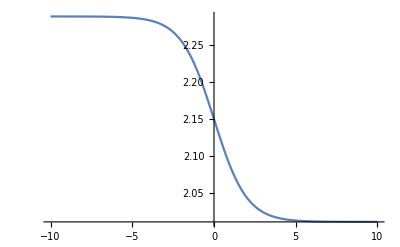

```mathematica
Plot[%,{x,-10,10}]
```